```mathematica
f[x_]:=x*(x+1)*(x-1)
```

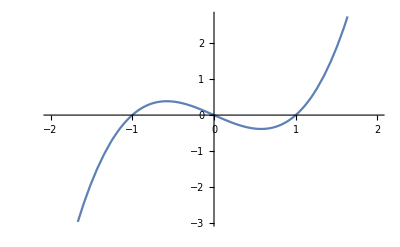

```mathematica
Plot[f[x],{x,-2,2},PlotLegends->"Expressions"]
```

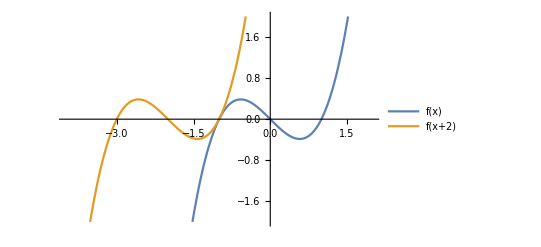

```mathematica
Plot[{f[x],f[x+2]},{x,-4,2},PlotRange->{Automatic,{-2,2}},PlotLegends->"Expressions"]
```

“Va 2 unidades adelantado” con respecto a f(x).

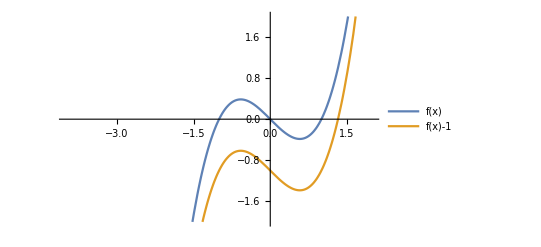

```mathematica
Plot[{f[x],f[x]-1},{x,-4,2},PlotRange->{Automatic,{-2,2}},PlotLegends->"Expressions"]
```

f(x) trasladado una unidad hacia abajo.

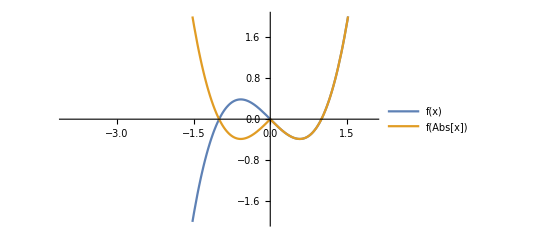

```mathematica
Plot[{f[x],f[Abs[x]]},{x,-4,2},PlotRange->{Automatic,{-2,2}},PlotLegends->"Expressions"]
```

f(x) cuando x es positivo, f(-x) cuando x es negativo. Es decir, la gráfica en el lado dcho. es como la de f(x), y en el lado izdo. es su “reflejo” en el eje y.

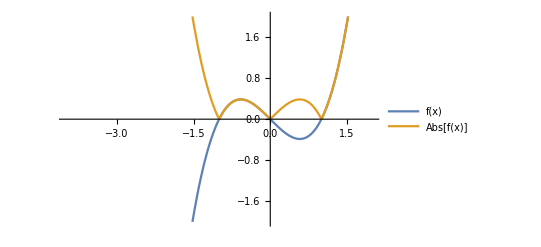

```mathematica
Plot[{f[x],Abs[f[x]]},{x,-4,2},PlotRange->{Automatic,{-2,2}},PlotLegends->"Expressions"]
```

f(x) cuando f(x) es positivo, -f(x) cuando f(x) es negativo. Es decir, si f(x) es negativo, “reflejamos” en el eje x.

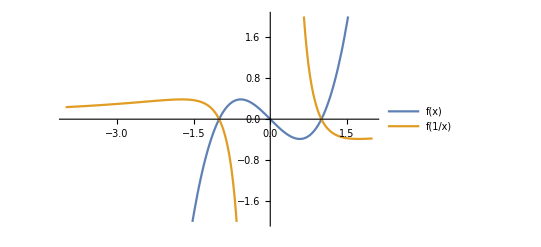

```mathematica
Plot[{f[x],f[1/x]},{x,-4,2},PlotRange->{Automatic,{-2,2}},PlotLegends->"Expressions"]
```